# 第一题

## 数据命名与赋值

### 总体数据

```mathematica
(*浮子质量 (kg)*)M=4866;
(*浮子底半径 (m)*)R=1;
(*浮子圆柱部分高度 (m)*)H1=3;
(*浮子圆锥部分高度 (m)*)H2=0.8;
(*振子质量 (kg)*)m=2433;
(*振子半径 (m)*)r=0.5;
(*振子高度 (m)*)h=0.5;
(*海水的密度 (kg/m.b3)*)ρ=1025;
(*重力加速度 (m/s.b2)*)g=9.8;
(*弹簧刚度 (N/m)*)kv=80000;
(*弹簧原长 (m)*)l0=0.5;
(*扭转弹簧刚度 (N·m)*)kh=250000;
(*静水恢复力矩系数 (N·m)*)kw=8890.7;
```

### 第一题专属数据

```mathematica
(*入射波浪频率*)ω1=1.4005;
(*(*入射波浪角速度*)ω1=2Pi f1;*)
(*垂荡附加质量*)m1=1335.535;
(*纵摇附加转动惯量*)L1=6779.315;
(*垂荡兴波阻尼系数*)Γv1=656.3616;
(*纵摇兴波阻尼系数*)Γh1=151.4388;
(*垂荡激励力振幅*)f=6250;
(*纵摇激励力矩振幅*)L=1230;
```

```mathematica
(*阻尼器阻尼力N·s/m*)kd=10000;
```

## 基础数据计算

### 初始条件

```mathematica
Clear["Global`*"]
```

```mathematica
(*初始吃水线距离圆柱底面的距离*)h0=x/.First@Solve[(M+m)g==ρ g ((Pi R^2 H2)/3+Pi R^2 x),x]
```

2.00001

```mathematica
Hg(*浮子重心(距离底面的高度)*)=With[{
m1=Pi R √(R^2+H2^2)(*圆锥"质量"*),
m2=2Pi R H1(*圆柱"质量"*),
h1=Integrate[x 2Pi x R/H2 √(R^2+H2^2)/H2,{x,0,H2}]/Integrate[2Pi x R/H2 √(R^2+H2^2)/H2,{x,0,H2}](*圆锥质心距离底面高度*),
h2=H1/2(*圆柱质心距离底面高度*)
},
(-m1 h1+m2 h2)/(m1+m2)
]
```

1.14235

```mathematica
x0(*弹簧的初始长度*)=x/.Solve[kv (l0-x)==m g,x][[1]]
```

0.201957

```mathematica
hg(*振子重心*)=With[{
l=x/.Solve[kv (l0-x)==m g,x][[1]]
},
l+h/2
]
```

0.451958

## 垂荡运动微分方程

### 各种力的函数

```mathematica
fd1[t_](*阻尼器阻尼力1*):=kd(x1'[t]-x2'[t]);
fd2[t_](*阻尼器阻尼力2*):=kd √Abs[x1'[t]-x2'[t]] (x1'[t]-x2'[t]);
bigVolume(*排水体积随大的位移*)[x_]:=Piecewise[{{(Pi R^2 H2)/3+Pi R^2 (h0-x),-(H1-h0)<x<=h0},{(H2+h0-x)^3/H2^3 (Pi R^2 H2)/3,x>h0}}];
fwaved[t_](*兴波阻尼力*):=-Γv1 x1'[t];
fb[x_]:=ρ g bigVolume[x];
```

### 运动方程&求解

#### 第一问

```mathematica
smallEqn(*振子运动方程*)[t_]:=m x2''[t]==fd1[t]+kv(l0-x0+x1[t]-x2[t])-m g;
bigEqn(*浮子运动方程*)[t_]:=(m1+M)x1''[t]==-fd1[t]-kv(l0-x0+x1[t]-x2[t])+fb[x1[t]]+f Cos[ω1 t]-M g+fwaved[t];
```

```mathematica
ans1=Flatten@NDSolve[{smallEqn[t],bigEqn[t],x1[0]==0,x2[0]==0,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},{t,0,300}];
big[x_](*浮子的运动函数, 位移*):=x1[t]/.ans1/.t->x;
small[x_](*振子位移*):=x2[t]/.ans1/.t->x;
```

```mathematica
Manipulate[
Show[
Plot[{big[t],small[t]},{t,a,a+15},PlotLegends->{"x1,浮子","x2,振子"}],
ContourPlot[y==0.5,{x,0,1000},{y,0,5}]
],
{a,0,200}]
```

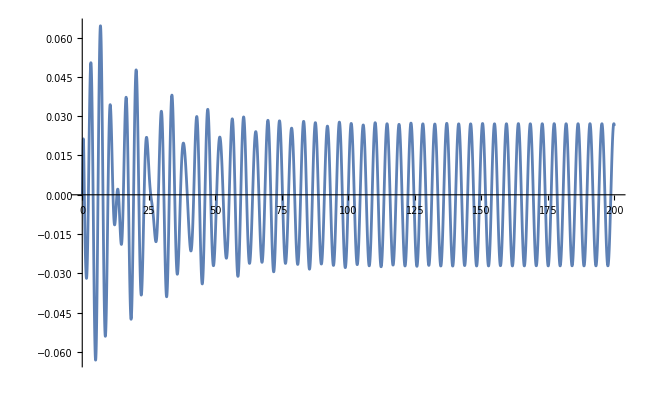

```mathematica
Plot[big[t]-small[t],{t,0,200},PlotPoints->200]
```

```mathematica
totalTime=(40 2Pi)/ω1;
data11={{{"时间","浮子位移","浮子速度","振子位移","振子速度"}}~Join~Table[{t,big[t],big'[t],small[t],small'[t]},{t,0,totalTime,10}]}[[1]]//Transpose
```

{{时间,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170},{浮子位移,0.,-0.190711,-0.590684,-0.310678,0.285375,0.24174,-0.314505,-0.384327,0.174899,0.405883,-0.083614,-0.437933,-0.0381859,0.423817,0.14732,-0.386613,-0.250243,0.320013},{浮子速度,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{振子位移,4.03897×10^-28,-0.211679,-0.634248,-0.339841,0.296499,0.258013,-0.331436,-0.411488,0.180588,0.431956,-0.0840673,-0.465158,-0.0455575,0.448691,0.160993,-0.408043,-0.269663,0.336263},{振子速度,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
With[{p=kd (D[ans1[[2,2]],t]-D[ans1[[1,2]],t])^2/.t->100},p]//AbsoluteTiming
```

{0.0004599,15.0469}

```mathematica
NIntegrate[kd (D[ans1[[2,2]],t]-D[ans1[[1,2]],t])^2,{t,0,100}]//AbsoluteTiming
```

{0.0395754,1254.59}

```mathematica
power1[100]//AbsoluteTiming
```

{0.0027953,15.047}

```mathematica
15.046989317657346
15.046924332859186
```

```mathematica
Export["data11.csv",data11]
```

data11.csv

#### 第二问

```mathematica
epsilon=1.0*^-8;

fd2Regularized[t_]:=With[{vrel=x1'[t]-x2'[t]},kd*vrel^2/Sqrt[Abs[vrel]+epsilon]];
```

```mathematica
smallEqn2[t_]:=m x2''[t]==fd2Regularized[t]+kv (l0-x0+x1[t]-x2[t])-m g;
bigEqn2[t_]:=(m1+M) x1''[t]==-fd2Regularized[t]-kv (l0-x0+x1[t]-x2[t])+fb[x1[t]]+f Cos[ω1 t]-M g+fwaved[t];
```

```mathematica
ans2=Flatten@NDSolve[{smallEqn2[t],bigEqn2[t],x1[0]==0,x2[0]==0,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},{t,0,300},PrecisionGoal->10];
big2[x_]:=x1[t]/.ans2/.t->x;
small2[x_](*振子位移*):=x2[t]/.ans2/.t->x;
```

```mathematica
ans2
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}

```mathematica
Manipulate[
Plot[{big2[t],small2[t]},{t,a,a+10},PlotLegends->{"x1,浮子","x2,振子"},PlotLabel->Style["第二问",FontFamily->"攸望漫画体",FontSize->30]],{a,0,90}]
```

```mathematica
totalTime=(80Pi)/ω1
```

179.455

```mathematica
data12={{"时间(s)","x1","v1","x2","v2"}}~Join~Transpose@Table[fun@#&/@Range[0,totalTime,10],{fun,{#&,big2,big2',small2,small2'}}]
```

{{时间(s),x1,v1,x2,v2},{0,0.,-5.42101×10^-20,0.,-2.06795×10^-25},{10,-0.21241,-0.704144,-0.247159,-0.652653},{20,-0.61783,-0.273339,-0.676558,-0.315269},{30,-0.33703,0.491102,-0.364923,0.449309},{40,0.258448,0.286354,0.288336,0.262446},{50,0.219193,-0.534658,0.240407,-0.498765},{60,-0.330662,-0.518023,-0.354758,-0.513021},{70,-0.394073,0.295437,-0.424201,0.328975},{80,0.170694,0.52707,0.173517,0.545168},{90,0.401412,-0.195353,0.422296,-0.260043},{100,-0.0902597,-0.606505,-0.0939466,-0.674486},{110,-0.44162,0.0234243,-0.468446,0.0157374},{120,-0.0398065,0.600516,-0.0385592,0.636706},{130,0.422333,0.116448,0.452383,0.142145},{140,0.144921,-0.584686,0.154453,-0.603234},{150,-0.388045,-0.284356,-0.413266,-0.296451},{160,-0.249479,0.496186,-0.265338,0.533827},{170,0.321461,0.410956,0.341291,0.433406}}

```mathematica
Dynamic@(data12//TableForm)
```

```mathematica
Export["data12.xlsx",{data12}]
```

data12.xlsx

```mathematica
Clear["Global`*"]
```

### 第一问解析解

```mathematica
bigVolume(*排水体积随大的位移*)[x_]:=(Pi R^2 H2)/3+Pi R^2 (h0-x);
```

```mathematica
smallEqn(*振子运动方程*)[t_]:=m x2''[t]==fd1[t]+kv(l0-x0+x1[t]-x2[t])-m g;
bigEqn(*浮子运动方程*)[t_]:=(m1+M)x1''[t]==-fd1[t]-kv(l0-x0+x1[t]-x2[t])+fb[x1[t]]+f Cos[ω1 t]-M g+fwaved[t];
```

```mathematica
aysysans1=DSolve[{smallEqn[t],bigEqn[t],x1[0]==0,x2[0]==0,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},t]
```

{{x1[t]→ⅇ^(-2.91425 t) ((-0.427765-2.77809×10^-18 ⅈ) ⅇ^(2.87121 t) Cos[1.88089 t]+(0.37235+7.35859×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[0.48039 t] Cos[1.88089 t]+(6.56665×10^-16+1.74775×10^-32 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t]^2+(0.00047579-5.32047×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[1.88089 t]^2+(0.0549395+1.08575×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Cos[3.28139 t]-(0.+7.22695×10^-20 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[4.84667 t]-(0.0064101-7.90921×10^-18 ⅈ) ⅇ^(0.0430423 t) Cos[6.24717 t]-(4.16334×10^-17+5.21801×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[0.48039 t] Cos[6.24717 t]-(9.86076×10^-32+9.0093×10^-33 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Cos[6.24717 t]-(6.16298×10^-33-7.78636×10^-35 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[6.24717 t]-(2.08709×10^-18+1.2238×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Cos[1.88089 t] Cos[6.24717 t]-(2.1684×10^-19-2.35703×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Cos[1.88089 t] Cos[6.24717 t]-(3.46945×10^-18+7.69907×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[3.28139 t] Cos[6.24717 t]+(0.00385408+4.39332×10^-20 ⅈ) ⅇ^(2.91425 t) Cos[4.84667 t] Cos[6.24717 t]+(3.50255×10^-17-4.64786×10^-33 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t]^2-(0.000336042+1.22938×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[6.24717 t]^2-(4.33681×10^-19+5.42301×10^-20 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[7.64767 t]+(0.00289206+3.29669×10^-20 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Cos[7.64767 t]-(0.033362+6.59319×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[0.48039 t]+(5.20417×10^-18+4.67526×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[0.48039 t]-(0.00443101-4.94606×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t]^2 Sin[1.4005 t]+(1.77809×10^-17+1.13831×10^-17 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Cos[6.24717 t] Sin[1.4005 t]+(3.38813×10^-20-7.1935×10^-20 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[6.24717 t] Sin[1.4005 t]+(0.0000959587+3.48875×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t]^2 Sin[1.4005 t]-(0.0281178-3.0472×10^-17 ⅈ) ⅇ^(2.87121 t) Sin[1.88089 t]-(0.00519796+6.27688×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[0.48039 t] Sin[1.88089 t]+(2.46519×10^-32-1.01815×10^-31 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[1.88089 t]+(0.0400476-6.58332×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[1.88089 t] Sin[1.88089 t]-(0.000766949+9.26142×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[3.28139 t] Sin[1.88089 t]-(1.73472×10^-18-7.07512×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[4.84667 t] Sin[1.88089 t]-(3.58223×10^-32+2.02603×10^-32 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[1.88089 t]-(6.54816×10^-33-8.97959×10^-33 ⅈ) ⅇ^(5.74241 t) Cos[6.24717 t] Sin[1.88089 t]-(2.64545×10^-17+1.53426×10^-17 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Cos[6.24717 t] Sin[1.88089 t]+(5.20417×10^-18+4.29679×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Cos[6.24717 t] Sin[1.88089 t]-(4.33681×10^-19-5.30908×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[7.64767 t] Sin[1.88089 t]+(0.00046573+5.624×10^-19 ⅈ) ⅇ^(2.91425 t) Sin[0.48039 t] Sin[1.88089 t]-(0.316955+1.83516×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[1.4005 t] Sin[1.88089 t]-(1.81604×10^-18+1.1706×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[1.4005 t] Sin[1.88089 t]-(8.67362×10^-19-1.18368×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[6.24717 t] Sin[1.4005 t] Sin[1.88089 t]+(6.56665×10^-16+2.01825×10^-32 ⅈ) ⅇ^(2.91425 t) Sin[1.88089 t]^2+(0.427289+1.08903×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Sin[1.88089 t]^2+(0.0326414+1.36415×10^-18 ⅈ) ⅇ^(2.91425 t) Sin[1.4005 t] Sin[1.88089 t]^2-(0.000720647+1.42418×10^-20 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[3.28139 t]+(8.13152×10^-20+1.00989×10^-20 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[3.28139 t]+(0.0000100601+1.21483×10^-20 ⅈ) ⅇ^(2.91425 t) Sin[1.88089 t] Sin[3.28139 t]+(0.+4.2813×10^-20 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[4.84667 t]-(0.00228319+2.60264×10^-20 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[4.84667 t]+(8.67362×10^-19-4.19135×10^-19 ⅈ) ⅇ^(5.74241 t) Sin[1.88089 t] Sin[4.84667 t]-(0.00404187+2.4506×10^-19 ⅈ) ⅇ^(0.0430423 t) Sin[6.24717 t]-(4.85723×10^-17-3.86809×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[0.48039 t] Sin[6.24717 t]-(9.86076×10^-32-9.26973×10^-33 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Sin[6.24717 t]-(1.54074×10^-33-2.23361×10^-33 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[6.24717 t]+(8.67362×10^-19-2.59715×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Cos[1.88089 t] Sin[6.24717 t]-(3.25261×10^-19-4.7198×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Cos[1.88089 t] Sin[6.24717 t]-(5.20417×10^-18-5.70729×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[3.28139 t] Sin[6.24717 t]+(0.00038443+1.08903×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[4.84667 t] Sin[6.24717 t]+(8.85928×10^-33-4.90404×10^-33 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[6.24717 t]+(0.00269607-2.78629×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[6.24717 t] Sin[6.24717 t]+(0.000288471+8.17198×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[7.64767 t] Sin[6.24717 t]+(5.20417×10^-18-3.46575×10^-19 ⅈ) ⅇ^(0.0860846 t) Sin[0.48039 t] Sin[6.24717 t]-(6.93889×10^-18-2.55029×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Sin[1.4005 t] Sin[6.24717 t]-(4.06576×10^-20-8.95355×10^-20 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[1.4005 t] Sin[6.24717 t]-(0.00108147+3.40126×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[1.4005 t] Sin[6.24717 t]+(2.46519×10^-32-3.17341×10^-33 ⅈ) ⅇ^(0.0860846 t) Sin[1.88089 t] Sin[6.24717 t]+(3.69779×10^-32+1.17481×10^-33 ⅈ) ⅇ^(5.74241 t) Sin[1.88089 t] Sin[6.24717 t]+(1.38778×10^-17-3.25601×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]+(1.04083×10^-17+8.60404×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]+(8.67362×10^-19-2.62263×10^-19 ⅈ) ⅇ^(0.0860846 t) Sin[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]+(1.30104×10^-18-1.4733×10^-19 ⅈ) ⅇ^(5.74241 t) Sin[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]+(9.48677×10^-20-7.48631×10^-21 ⅈ) ⅇ^(0.0860846 t) Sin[3.28139 t] Sin[6.24717 t]-(0.000227739+6.45153×10^-19 ⅈ) ⅇ^(2.91425 t) Sin[4.84667 t] Sin[6.24717 t]+(3.50255×10^-17-5.90611×10^-33 ⅈ) ⅇ^(2.91425 t) Sin[6.24717 t]^2+(0.00674614-6.49879×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Sin[6.24717 t]^2+(0.00119741-1.17134×10^-19 ⅈ) ⅇ^(2.91425 t) Sin[1.4005 t] Sin[6.24717 t]^2+(2.1684×10^-19+2.03599×10^-20 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[7.64767 t]-(0.00108578+1.23769×10^-20 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[7.64767 t]+(2.1684×10^-19-1.99321×10^-19 ⅈ) ⅇ^(5.74241 t) Sin[1.88089 t] Sin[7.64767 t]-(0.000108302+3.06805×10^-19 ⅈ) ⅇ^(2.91425 t) Sin[6.24717 t] Sin[7.64767 t]),x2[t]→ⅇ^(-2.91425 t) ((-0.476244+3.18587×10^-18 ⅈ) ⅇ^(2.87121 t) Cos[1.88089 t]+(0.415268+9.57841×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[0.48039 t] Cos[1.88089 t]+(7.32056×10^-16+6.84966×10^-33 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t]^2-(0.000296738+4.63795×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[1.88089 t]^2+(0.0612721+1.41328×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Cos[3.28139 t]-(4.33681×10^-19-3.90984×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[4.84667 t]+(0.015786-3.29549×10^-18 ⅈ) ⅇ^(0.0430423 t) Cos[6.24717 t]-(0.+3.63207×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[0.48039 t] Cos[6.24717 t]+(9.86076×10^-32-6.92895×10^-33 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Cos[6.24717 t]-(6.16298×10^-33-1.17058×10^-33 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[6.24717 t]+(4.63496×10^-18+3.88367×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Cos[1.88089 t] Cos[6.24717 t]-(2.57498×10^-19+4.50522×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Cos[1.88089 t] Cos[6.24717 t]-(0.+5.35905×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[3.28139 t] Cos[6.24717 t]-(0.0091383-4.92955×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[4.84667 t] Cos[6.24717 t]-(8.58403×10^-17-1.69873×10^-32 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t]^2+(0.00020958+2.83599×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[6.24717 t]^2+(0.+2.93389×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[7.64767 t]-(0.00685727-3.69907×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Cos[7.64767 t]-(0.0372075+8.58213×10^-20 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[0.48039 t]-(3.46945×10^-18-3.25428×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[0.48039 t]+(0.0027635+4.32197×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t]^2 Sin[1.4005 t]-(3.85976×10^-17+3.6158×10^-17 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Cos[6.24717 t] Sin[1.4005 t]+(6.43745×10^-20+1.17638×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Cos[6.24717 t] Sin[1.4005 t]-(0.0000598469+8.04948×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t]^2 Sin[1.4005 t]-(0.0417314-1.24242×10^-17 ⅈ) ⅇ^(2.87121 t) Sin[1.88089 t]+(0.00324183+1.24003×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[0.48039 t] Sin[1.88089 t]+(3.69779×10^-32-5.4155×10^-32 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[1.88089 t]+(0.0342911-5.74033×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[1.88089 t] Sin[1.88089 t]+(0.000478326+1.82965×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[3.28139 t] Sin[1.88089 t]-(1.73472×10^-18-6.13921×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[4.84667 t] Sin[1.88089 t]+(8.01187×10^-32+6.71983×10^-32 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[1.88089 t]-(8.47409×10^-33-7.54601×10^-33 ⅈ) ⅇ^(5.74241 t) Cos[6.24717 t] Sin[1.88089 t]+(5.76796×10^-17+4.86889×10^-17 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Cos[6.24717 t] Sin[1.88089 t]+(3.46945×10^-18+3.11899×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Cos[6.24717 t] Sin[1.88089 t]-(4.33681×10^-19-4.60679×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[7.64767 t] Sin[1.88089 t]-(0.000290463+1.11105×10^-18 ⅈ) ⅇ^(2.91425 t) Sin[0.48039 t] Sin[1.88089 t]-(0.354281+1.7126×10^-17 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[1.4005 t] Sin[1.88089 t]+(3.98444×10^-18+3.71837×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[1.4005 t] Sin[1.88089 t]-(8.67362×10^-19-1.79593×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[6.24717 t] Sin[1.4005 t] Sin[1.88089 t]+(7.32056×10^-16+1.74507×10^-32 ⅈ) ⅇ^(2.91425 t) Sin[1.88089 t]^2+(0.476541+9.30091×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Sin[1.88089 t]^2+(0.0364038+1.30412×10^-18 ⅈ) ⅇ^(2.91425 t) Sin[1.4005 t] Sin[1.88089 t]^2-(0.000803712+1.85381×10^-21 ⅈ) ⅇ^(2.91425 t) Cos[1.88089 t] Sin[3.28139 t]+(0.+7.02951×10^-21 ⅈ) ⅇ^(0.0860846 t) Cos[6.24717 t] Sin[3.28139 t]-(6.27424×10^-6+2.39997×10^-20 ⅈ) ⅇ^(2.91425 t) Sin[1.88089 t] Sin[3.28139 t]-(2.1684×10^-19+2.31622×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[4.84667 t]+(0.0054136-2.92031×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[4.84667 t]+(4.33681×10^-19-3.63692×10^-19 ⅈ) ⅇ^(5.74241 t) Sin[1.88089 t] Sin[4.84667 t]+(0.00840773-2.3373×10^-17 ⅈ) ⅇ^(0.0430423 t) Sin[6.24717 t]+(5.55112×10^-17+1.17316×10^-17 ⅈ) ⅇ^(0.0860846 t) Cos[0.48039 t] Sin[6.24717 t]+(1.2326×10^-31+1.49855×10^-32 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Sin[6.24717 t]-(3.08149×10^-33+7.2107×10^-33 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[6.24717 t]-(1.73472×10^-18-4.97711×10^-19 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Cos[1.88089 t] Sin[6.24717 t]-(4.87891×10^-19+9.02141×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Cos[1.88089 t] Sin[6.24717 t]+(6.93889×10^-18+1.73097×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[3.28139 t] Sin[6.24717 t]-(0.000239759+2.40539×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[4.84667 t] Sin[6.24717 t]-(2.61926×10^-32-8.73868×10^-33 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[6.24717 t]-(0.00756839-6.24027×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Cos[6.24717 t] Sin[6.24717 t]-(0.000179912+1.80498×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[7.64767 t] Sin[6.24717 t]-(6.93889×10^-18+1.05113×10^-18 ⅈ) ⅇ^(0.0860846 t) Sin[0.48039 t] Sin[6.24717 t]+(2.77556×10^-17-4.94728×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[1.88089 t] Sin[1.4005 t] Sin[6.24717 t]-(5.0822×10^-20+1.4642×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[1.4005 t] Sin[6.24717 t]+(0.00235553+8.37842×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[1.4005 t] Sin[6.24717 t]-(4.93038×10^-32-5.13392×10^-33 ⅈ) ⅇ^(0.0860846 t) Sin[1.88089 t] Sin[6.24717 t]+(0.+2.04408×10^-34 ⅈ) ⅇ^(5.74241 t) Sin[1.88089 t] Sin[6.24717 t]-(2.77556×10^-17-6.23972×10^-18 ⅈ) ⅇ^(0.0860846 t) Cos[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]+(1.04083×10^-17+6.24558×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]-(3.46945×10^-18-5.08762×10^-19 ⅈ) ⅇ^(0.0860846 t) Sin[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]+(4.33681×10^-19-2.23535×10^-19 ⅈ) ⅇ^(5.74241 t) Sin[1.4005 t] Sin[1.88089 t] Sin[6.24717 t]-(1.0842×10^-19+2.27053×10^-20 ⅈ) ⅇ^(0.0860846 t) Sin[3.28139 t] Sin[6.24717 t]+(0.000142035+1.42497×10^-18 ⅈ) ⅇ^(2.91425 t) Sin[4.84667 t] Sin[6.24717 t]-(8.58403×10^-17-1.167×10^-32 ⅈ) ⅇ^(2.91425 t) Sin[6.24717 t]^2-(0.0159956-1.12412×10^-18 ⅈ) ⅇ^(2.91425 t) Cos[1.4005 t] Sin[6.24717 t]^2-(0.00283914-2.04192×10^-19 ⅈ) ⅇ^(2.91425 t) Sin[1.4005 t] Sin[6.24717 t]^2+(2.1684×10^-19-1.10149×10^-19 ⅈ) ⅇ^(5.74241 t) Cos[1.88089 t] Sin[7.64767 t]+(0.00257446-1.38876×10^-19 ⅈ) ⅇ^(2.91425 t) Cos[6.24717 t] Sin[7.64767 t]-(0.+1.72955×10^-19 ⅈ) ⅇ^(5.74241 t) Sin[1.88089 t] Sin[7.64767 t]+(0.0000675453+6.77652×10^-19 ⅈ) ⅇ^(2.91425 t) Sin[6.24717 t] Sin[7.64767 t])}}

```mathematica
big1[t_]:=;
small1[t_]:=;
```

```mathematica
Chop[aysysans1[[1,2,2]]]
```

ⅇ^(-2.91425 t) (-0.476244 ⅇ^(2.87121 t) Cos[1.88089 t]+0.415268 ⅇ^(2.91425 t) Cos[0.48039 t] Cos[1.88089 t]-0.000296738 ⅇ^(2.91425 t) Cos[1.4005 t] Cos[1.88089 t]^2+0.0612721 ⅇ^(2.91425 t) Cos[1.88089 t] Cos[3.28139 t]+0.015786 ⅇ^(0.0430423 t) Cos[6.24717 t]-0.0091383 ⅇ^(2.91425 t) Cos[4.84667 t] Cos[6.24717 t]+0.00020958 ⅇ^(2.91425 t) Cos[1.4005 t] Cos[6.24717 t]^2-0.00685727 ⅇ^(2.91425 t) Cos[6.24717 t] Cos[7.64767 t]-0.0372075 ⅇ^(2.91425 t) Cos[1.88089 t] Sin[0.48039 t]+0.0027635 ⅇ^(2.91425 t) Cos[1.88089 t]^2 Sin[1.4005 t]-0.0000598469 ⅇ^(2.91425 t) Cos[6.24717 t]^2 Sin[1.4005 t]-0.0417314 ⅇ^(2.87121 t) Sin[1.88089 t]+0.00324183 ⅇ^(2.91425 t) Cos[0.48039 t] Sin[1.88089 t]+0.0342911 ⅇ^(2.91425 t) Cos[1.4005 t] Cos[1.88089 t] Sin[1.88089 t]+0.000478326 ⅇ^(2.91425 t) Cos[3.28139 t] Sin[1.88089 t]-0.000290463 ⅇ^(2.91425 t) Sin[0.48039 t] Sin[1.88089 t]-0.354281 ⅇ^(2.91425 t) Cos[1.88089 t] Sin[1.4005 t] Sin[1.88089 t]+0.476541 ⅇ^(2.91425 t) Cos[1.4005 t] Sin[1.88089 t]^2+0.0364038 ⅇ^(2.91425 t) Sin[1.4005 t] Sin[1.88089 t]^2-0.000803712 ⅇ^(2.91425 t) Cos[1.88089 t] Sin[3.28139 t]-6.27424×10^-6 ⅇ^(2.91425 t) Sin[1.88089 t] Sin[3.28139 t]+0.0054136 ⅇ^(2.91425 t) Cos[6.24717 t] Sin[4.84667 t]+0.00840773 ⅇ^(0.0430423 t) Sin[6.24717 t]-0.000239759 ⅇ^(2.91425 t) Cos[4.84667 t] Sin[6.24717 t]-0.00756839 ⅇ^(2.91425 t) Cos[1.4005 t] Cos[6.24717 t] Sin[6.24717 t]-0.000179912 ⅇ^(2.91425 t) Cos[7.64767 t] Sin[6.24717 t]+0.00235553 ⅇ^(2.91425 t) Cos[6.24717 t] Sin[1.4005 t] Sin[6.24717 t]+0.000142035 ⅇ^(2.91425 t) Sin[4.84667 t] Sin[6.24717 t]-0.0159956 ⅇ^(2.91425 t) Cos[1.4005 t] Sin[6.24717 t]^2-0.00283914 ⅇ^(2.91425 t) Sin[1.4005 t] Sin[6.24717 t]^2+0.00257446 ⅇ^(2.91425 t) Cos[6.24717 t] Sin[7.64767 t]+0.0000675453 ⅇ^(2.91425 t) Sin[6.24717 t] Sin[7.64767 t])

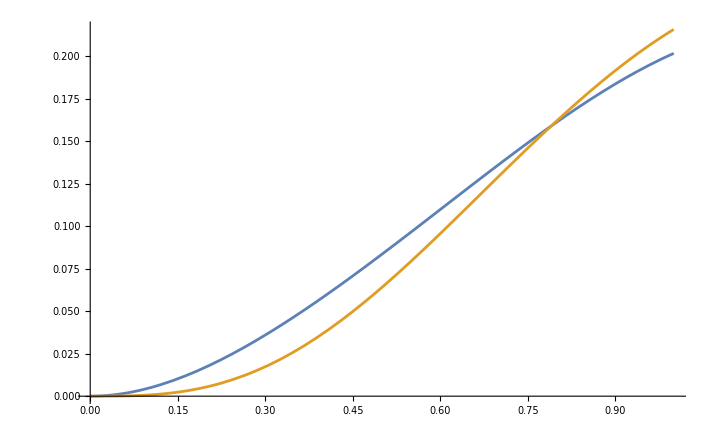

```mathematica
Plot[{big1[t],small1[t]},{t,0,1}]
```

```mathematica
power1[t_]:=kd (big1'[t]-small1'[t])^2//FullSimplify
```

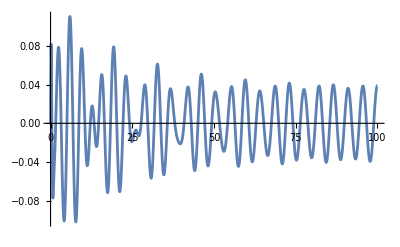

```mathematica
Plot[big1'[t]-small1'[t],{t,0,100}]
```

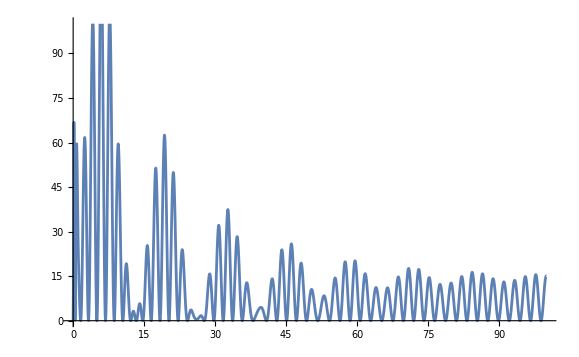
{6.51061,-Graphics-}

```mathematica
Plot[power1[t],{t,0,100},PlotRange->{{0,100},{0,100}}]//AbsoluteTiming
```

#### 数值&解析尝试(失败)

```mathematica
NIntegrate[power1[t],{t,0,totalTime}]//AbsoluteTiming
```

NIntegrate::ncvb: 在接近 {t} = {127.929} 处的 t 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1456.49 和 0.379271.

{5.90268,1456.49}

```mathematica
power1[t]
```

5.53144 ⅇ^(-5.82849 t) (ⅇ^(2.87121 t) (1. Cos[1.88089 t]-3.90191 Sin[1.88089 t])+ⅇ^(0.0430423 t) (-0.597188 Cos[6.24717 t]+7.41562 Sin[6.24717 t])+ⅇ^(2.91425 t) (-0.402812 Cos[1.4005 t]-2.2482×10^-15 Cos[2.36128 t]-1.47105×10^-15 Cos[5.16228 t]-4.44089×10^-16 Cos[13.8948 t]+1.56506 Sin[1.4005 t]+4.88498×10^-15 Sin[5.16228 t]+8.88178×10^-16 Sin[13.8948 t]))^2

```mathematica
Integrate[5.531437378134261 ⅇ^(-5.828494647264302 t) (ⅇ^(2.871205031135246 t) (1. Cos[1.8808898765054405 t]-3.9019087712986993 Sin[1.8808898765054405 t])+ⅇ^(0.04304229249690475 t) (-0.5971880079000682 Cos[6.247170360354152 t]+7.415623771002246 Sin[6.247170360354152 t])+ⅇ^(2.914247323632151 t) (-0.40281199209990454 Cos[1.4005 t]-2.248201624865942*^-15 Cos[2.361279753010881 t]-1.4710455076283326*^-15 Cos[5.162279753010881 t]-4.440892098500626*^-16 Cos[13.894840720708306 t]+1.56506483683191 Sin[1.4005 t]+4.884981308350689*^-15 Sin[5.162279753010881 t]+8.881784197001252*^-16 Sin[13.894840720708306 t]))^2,{t,0,totalTime}]//AbsoluteTiming
```

{6.66624,1829.03+8.49879×10^-17 ⅈ}

#### 数据导出

```mathematica
totalTime=(40 2Pi)/ω1
```

179.455

```mathematica
data11={{{"时间(s)","浮子位移(m)","浮子速度(m/s)","振子位移(m)","振子速度(m/s)"},Table[0,5]}~Join~Table[{t,big1[t],big1'[t],small1[t],small1'[t]},{t,0.2,totalTime,0.2}]}
```

```mathematica
Export["data11.xlsx",data11]
```

Export::fmterr: 无效的 XLSX 格式.

$Failed

# 第三题

## 数据命名与赋值

```mathematica
Clear["Global`*"]
```

### 总体数据

```mathematica
(*浮子质量 (kg)*)M=4866;
(*浮子底半径 (m)*)R=1;
(*浮子圆柱部分高度 (m)*)H1=3;
(*浮子圆锥部分高度 (m)*)H2=0.8;
(*振子质量 (kg)*)m=2433;
(*振子半径 (m)*)r=0.5;
(*振子高度 (m)*)h=0.5;
(*海水的密度 (kg/m.b3)*)ρ=1025;
(*重力加速度 (m/s.b2)*)g=9.8;
(*弹簧刚度 (N/m)*)kv=80000;
(*弹簧原长 (m)*)l0=0.5;
(*扭转弹簧刚度 (N·m)*)kh=250000;
(*静水恢复力矩系数 (N·m)*)kw=8890.7;
```

### 第三题专属数据

```mathematica
(*入射波浪频率 (s^-1)*)ω=1.7152;
(*垂荡附加质量 (Kg)*)mi=1028.876;
(*纵摇附加转动惯量 (Kg·m^2)*)Ji=7001.914;
(*垂荡兴波阻尼系数 (N·s/m)*)Γv1=683.4558;
(*纵摇兴波阻尼系数 (N·m·s)*)Γh1=654.3383;
(*垂荡激励力振幅 (N)*)f=3640;
(*纵摇激励力矩振幅 (N·m)*)L=1690;
(*直线阻尼器系数N s/m*)kdv=10000;
(*旋转阻尼器系数*)kdh=1000;
```

### 自算数据

```mathematica
Hg(*浮子重心(距离底面的高度)*)=With[{m1=π R √(R^2+H2^2),m2=2 π R H1,m3=π R^2,h1=-(∫_0^H2 (x 2 π x R √(R^2+H2^2))/(H2 H2)ⅆx)/(∫_0^H2 (2 π x R √(R^2+H2^2))/(H2 H2)ⅆx),h2=H1/2,h3=H1},(m1 h1+m2 h2+m3 h3)/(m1+m2+m3)];
σ=M/(2Pi R H1+Pi R^2+π R √(R^2+H2^2));
J1=With[{M1=σ π R √(R^2+H2^2)},M1 (R^2/4+H2^2/18)+M1 (Hg-H2/3)^2+2 π R H1 σ (R^2/2+H1^2/12+(Hg-H1/2)^2)+σ π R^2 (R^2/4+(H1-Hg)^2)];
(*初始吃水线距离圆柱底面的距离*)h0=x/.First@Solve[(M+m)g==ρ g ((Pi R^2 H2)/3+Pi R^2 x),x];
x0(*弹簧的初始长度*)=x/.Solve[kv (l0-x)==m g,x][[1]];
totalTime=(40 2Pi)/ω;
```

## 微扰方程

```mathematica
smallHeaveApp[t_]:=kdv(x1'[t]-x2'[t])+kv(l0-x0+x1[t]-x2[t])-m g ==m x2''[t];
smallSpinApp[t_]:=2kdh(th1'[t]-th2'[t])+kh (th1[t]-th2[t])==((1/4 m R^2+1/12 m h^2)+m(x2[t]+h/2)^2) th2''[t];
bigHeaveApp[t_]:=f Cos[ω t]-M g+ρ g( (Pi R^2 H2)/3+Pi R^2 (h0-x1[t]))-kdv(x1'[t]-x2'[t])-kv(l0-x0+x1[t]-x2[t])-Γv1 x1'[t]==(M+mi)x1''[t];
bigSpinApp[t_]:=-2kdh(th1'[t]-th2'[t])-kh (th1[t]-th2[t])+L Cos[ω t]+-Γh1 th1'[t]+-kw th1[t]==(J1+Ji)th1''[t];
```

```mathematica
eqnsApp[t_]:={smallHeaveApp[t],smallSpinApp[t],bigHeaveApp[t],bigSpinApp[t]}
```

```mathematica
eqnsApp[t]
```

{-23843.4+80000 (0.298043+x1[t]-x2[t])+10000 (x1'[t]-x2'[t])==2433 x2''[t],250000 (th1[t]-th2[t])+2000 (th1'[t]-th2'[t])==(658.938+2433 (0.25+x2[t])^2) th2''[t],-47686.8+3640 Cos[1.7152 t]+10045. (0.837758+π (2.00001-x1[t]))-80000 (0.298043+x1[t]-x2[t])-683.456 x1'[t]-10000 (x1'[t]-x2'[t])==5894.88 x1''[t],1690 Cos[1.7152 t]-8890.7 th1[t]-250000 (th1[t]-th2[t])-654.338 th1'[t]-2000 (th1'[t]-th2'[t])==14311.9 th1''[t]}

```mathematica
movesApp=NDSolve[eqnsApp[t]~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},{t,0,200},MaxStepSize->0.01]
```

{{x1→InterpolatingFunction[{{0., 200.}}, <>],x2→InterpolatingFunction[{{0., 200.}}, <>],th1→InterpolatingFunction[{{0., 200.}}, <>],th2→InterpolatingFunction[{{0., 200.}}, <>]}}

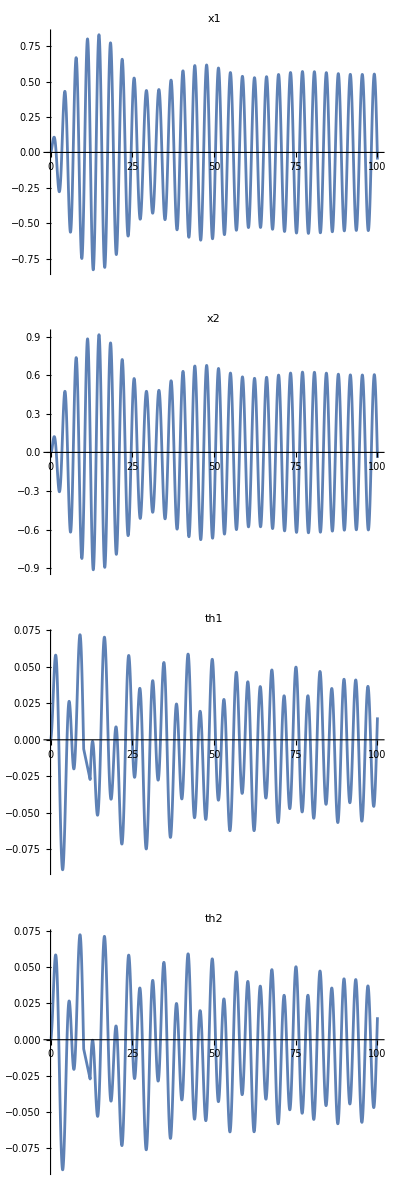

```mathematica
Plot[#[[2]][t],{t,0,100},PlotLabel->#[[1]]]&/@movesApp[[1]]//Column
```

```mathematica
With[{x1=movesApp[[1,1,2]],x2=movesApp[[1,2,2]],th1=movesApp[[1,3,2]],th2=movesApp[[1,4,2]]},
{{"时间","浮子位移","浮子速度","振子位移","振子速度","浮子角位移","浮子角速度","振子角位移","振子角速度"}}~Join~Table[Join[{t},{#[t],#'[t]}&/@{x1,x2,th1,th2}]//Flatten,{t,{10,20,40,60,100}}]
]//TableForm
```

时间 | 浮子位移 | 浮子速度 | 振子位移 | 振子速度 | 浮子角位移 | 浮子角速度 | 振子角位移 | 振子角速度
10 | -0.528276 | 0.969851 | -0.598729 | 1.0382 | 0.0082479 | -0.104753 | 0.00829687 | -0.105806
20 | -0.704815 | -0.269306 | -0.772294 | -0.319025 | 0.00887081 | 0.0024973 | 0.00946977 | 0.00317873
40 | 0.369361 | 0.75758 | 0.392653 | 0.844962 | -0.039117 | -0.0186167 | -0.0398676 | -0.0204609
60 | -0.320675 | -0.721762 | -0.341426 | -0.799321 | 0.0321231 | 0.0423418 | 0.0323952 | 0.0428951
100 | -0.050154 | -0.94669 | -0.0426118 | -1.03653 | 0.0153622 | 0.0730586 | 0.0155017 | 0.0735211

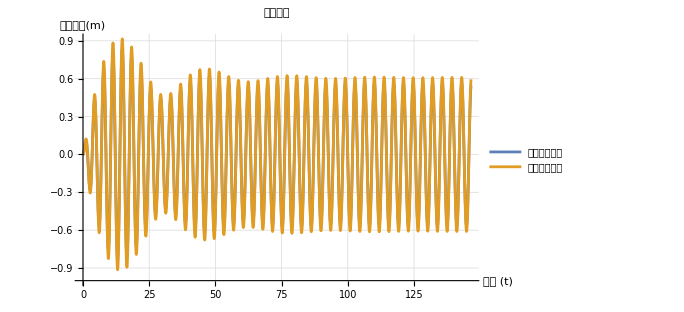

```mathematica
With[{x1=movesApp[[1,1,2]],x2=movesApp[[1,2,2]],th1=movesApp[[1,3,2]],th2=movesApp[[1,4,2]]},
Plot[{x1[t],x2[t]},{t,0,(40 2Pi)/ω},AxesLabel->(Style[#,FontFamily->"Times New Roman"]&/@{"时间 (t)","垂荡位移(m)"}),AxesOrigin->{0,-1},GridLines->Automatic,PlotLegends->Reverse@{"振子垂荡位移","浮子垂荡位移"},PlotLabel->Style["垂荡位移",FontFamily->"宋体",FontSize->20]]
]//TableForm
```

# 第四题

## 数据更新

```mathematica
(*入射波浪频率 (s^-1)*)ω=1.9806;
(*垂荡附加质量 (Kg)*)mi=1091.099;
(*纵摇附加转动惯量 (Kg·m^2)*)Ji=7142.493;
(*垂荡兴波阻尼系数 (N·s/m)*)Γv1=528.5018;
(*纵摇兴波阻尼系数 (N·m·s)*)Γh1=1655.909;
(*垂荡激励力振幅 (N)*)f=1760;
(*纵摇激励力矩振幅 (N·m)*)L=2140;

Hg(*浮子重心(距离底面的高度)*)=With[{m1=π R √(R^2+H2^2),m2=2 π R H1,m3=π R^2,h1=-(∫_0^H2 (x 2 π x R √(R^2+H2^2))/(H2 H2)ⅆx)/(∫_0^H2 (2 π x R √(R^2+H2^2))/(H2 H2)ⅆx),h2=H1/2,h3=H1},(m1 h1+m2 h2+m3 h3)/(m1+m2+m3)];
σ=M/(2Pi R H1+Pi R^2+π R √(R^2+H2^2));
J1=With[{M1=σ π R √(R^2+H2^2)},M1 (R^2/4+H2^2/18)+M1 (Hg-H2/3)^2+2 π R H1 σ (R^2/2+H1^2/12+(Hg-H1/2)^2)+σ π R^2 (R^2/4+(H1-Hg)^2)];
(*初始吃水线距离圆柱底面的距离*)h0=x/.First@Solve[(M+m)g==ρ g ((Pi R^2 H2)/3+Pi R^2 x),x];
x0(*弹簧的初始长度*)=x/.Solve[kv (l0-x)==m g,x][[1]];
totalTime=(40 2Pi)/ω;
```

## 微扰方程

```mathematica
smallHeaveApp4[t_]:=kdv(x1'[t]-x2'[t])+kv(l0-x0+x1[t]-x2[t])-m g ==m x2''[t];
smallSpinApp4[t_]:=2kdh(th1'[t]-th2'[t])+kh (th1[t]-th2[t])==((1/4 m R^2+1/12 m h^2)+m(x2[t]+h/2)^2) th2''[t];
bigHeaveApp4[t_]:=f Cos[ω t]-M g+ρ g( (Pi R^2 H2)/3+Pi R^2 (h0-x1[t]))-kdv(x1'[t]-x2'[t])-kv(l0-x0+x1[t]-x2[t])-Γv1 x1'[t]==(M+mi)x1''[t];
bigSpinApp4[t_]:=-2kdh(th1'[t]-th2'[t])-kh (th1[t]-th2[t])+L Cos[ω t]+-Γh1 th1'[t]+-kw th1[t]==(J1+Ji)th1''[t];
```

```mathematica
eqnsApp4[t_]:={smallHeaveApp4[t],smallSpinApp4[t],bigHeaveApp4[t],bigSpinApp4[t]}
```

```mathematica
kdh=100000
kdv=100000
```

100000

100000

```mathematica
movesApp4=NDSolve[eqnsApp4[t]~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},{t,0,200},MaxStepSize->0.01]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],th1→InterpolatingFunction[…],th2→InterpolatingFunction[…]}}

```mathematica
Dynamic[Plot[#[[2]][t],{t,0,100},PlotLabel->#[[1]]]&/@movesApp4[[1]]//Column]
```

## 计算

```mathematica
With[{x1=movesApp4[[1,1,2]],x2=movesApp4[[1,2,2]],th1=movesApp4[[1,3,2]],th2=movesApp4[[1,4,2]]},
Manipulate[
Plot[kdh (th1'[t]-th2'[t])^2,{t,a,a+5}],
{a,0,150}]
]
```

```mathematica
workVaule[kdvx_,kdhx_]:=(
NIntegrate[kdvx(#1'[t]-#2'[t])^2+2kdhx(#3'[t]-#4'[t])^2,{t,30 (2Pi)/ω,40 (2Pi)/ω}]&@@
(Last/@NDSolve[{
-23843.4+80000 (0.2980425+x1[t]-x2[t])+kdvx (x1'[t]-x2'[t])==2433 x2''[t],250000 (th1[t]-th2[t])+2 kdhx (th1'[t]-th2'[t])==(658.9375+2433 (0.25+x2[t])^2) th2''[t],-47686.8+1760 Cos[1.9806 t]+10045. (0.8377580409572781+π (2.0000102691923467-x1[t]))-80000 (0.2980425+x1[t]-x2[t])-528.5018 x1'[t]-kdvx (x1'[t]-x2'[t])==5957.099 x1''[t],2140 Cos[1.9806 t]-8890.7 th1[t]-250000 (th1[t]-th2[t])-1655.909 th1'[t]-2 kdhx (th1'[t]-th2'[t])==14452.49157401844 th1''[t]
}~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},{t,30 (2Pi)/ω,40 (2Pi)/ω},Method->"StiffnessSwitching"][[1]]))
```

```mathematica
workVaule[1000,2]
```

438.225

```mathematica
Table[workVaule[x,y],{x,1,1*^5,1*^3},{y,1,1*^5,1*^3}]
```

```mathematica
a=
```

{24.5456,{{1.46345,8.3903,12.6726,15.1594,16.4827,17.0017,16.985,16.6372,16.1025,15.4759},{12145.8,12151.8,12155.6,12157.6,12159.,12159.4,12159.4,12159.1,12158.7,12158.1},{20295.9,20301.6,20305.2,20307.3,20308.4,20308.9,20308.8,20308.6,20308.1,20307.6},{25181.4,25187.1,25190.7,25192.8,25193.8,25194.3,25194.2,25193.9,25193.4,25192.9},{27734.8,27740.8,27744.5,27746.5,27747.6,27748.,27748.,27747.7,27747.2,27746.7},{28760.,28766.3,28770.1,28772.2,28773.2,28773.6,28773.6,28773.2,28772.8,28772.2},{28840.5,28847.2,28851.1,28853.2,28854.3,28854.7,28854.6,28854.3,28853.8,28853.2},{28364.4,28371.5,28375.5,28377.7,28378.8,28379.1,28379.1,28378.7,28378.1,28377.5},{27577.5,27585.,27589.1,27591.4,27592.5,27592.9,27592.7,27592.3,27591.8,27591.1},{26631.7,26639.5,26643.8,26646.,26647.2,26647.5,26647.4,26647.,26646.4,26645.7}}}

```mathematica
a[[2]]//MatrixForm
```

(1.46345 | 8.3903 | 12.6726 | 15.1594 | 16.4827 | 17.0017 | 16.985 | 16.6372 | 16.1025 | 15.4759
12145.8 | 12151.8 | 12155.6 | 12157.6 | 12159. | 12159.4 | 12159.4 | 12159.1 | 12158.7 | 12158.1
20295.9 | 20301.6 | 20305.2 | 20307.3 | 20308.4 | 20308.9 | 20308.8 | 20308.6 | 20308.1 | 20307.6
25181.4 | 25187.1 | 25190.7 | 25192.8 | 25193.8 | 25194.3 | 25194.2 | 25193.9 | 25193.4 | 25192.9
27734.8 | 27740.8 | 27744.5 | 27746.5 | 27747.6 | 27748. | 27748. | 27747.7 | 27747.2 | 27746.7
28760. | 28766.3 | 28770.1 | 28772.2 | 28773.2 | 28773.6 | 28773.6 | 28773.2 | 28772.8 | 28772.2
28840.5 | 28847.2 | 28851.1 | 28853.2 | 28854.3 | 28854.7 | 28854.6 | 28854.3 | 28853.8 | 28853.2
28364.4 | 28371.5 | 28375.5 | 28377.7 | 28378.8 | 28379.1 | 28379.1 | 28378.7 | 28378.1 | 28377.5
27577.5 | 27585. | 27589.1 | 27591.4 | 27592.5 | 27592.9 | 27592.7 | 27592.3 | 27591.8 | 27591.1
26631.7 | 26639.5 | 26643.8 | 26646. | 26647.2 | 26647.5 | 26647.4 | 26647. | 26646.4 | 26645.7)

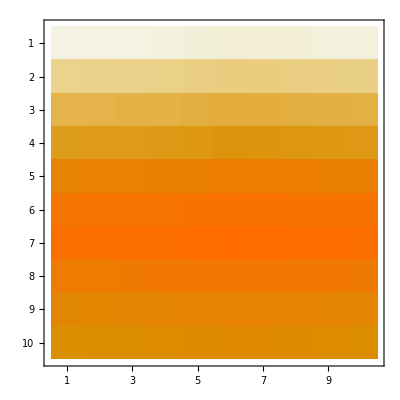

```mathematica
MatrixPlot[a[[2]]]
```

```mathematica
a[[2,6,7]]
```

28773.6

```mathematica
workVaule[1*^5,1*^5]
```

9064.85

```mathematica
Clear[getPower]
```

```mathematica
getPower[kdvx_,kdhx_]:=getPower[kdvx,kdhx]=workVaule[kdvx,kdhx]/(20 Pi/ω)
```

```mathematica
startPoints={#1,#2,getPower[#1,#2]}&@@#&/@(Table[{i,j},{i,0,1*^5,1000},{j,0,1*^5,1000}]//Flatten[#,1]&)
```

NIntegrate::ncvs: NIntegrate 无法在 t = 126.895 处收敛到接近显著的不可积奇点.

General::stop: 在本次计算中，NIntegrate::ncvs 的进一步输出将被抑制.

```mathematica
Manipulate[
Column[{
Plot[kdvx(#1'[t]-#2'[t])^2+2kdhx(#3'[t]-#4'[t])^2,{t,30 (2Pi)/ω,40 (2Pi)/ω}]&@@(Last/@NDSolve[{-23843.4+80000 (0.2980425+x1[t]-x2[t])+kdvx (x1'[t]-x2'[t])==2433 x2''[t],250000 (th1[t]-th2[t])+2 kdhx (th1'[t]-th2'[t])==(658.9375+2433 (0.25+x2[t])^2) th2''[t],-47686.8+1760 Cos[1.9806 t]+10045. (0.8377580409572781+π (2.0000102691923467-x1[t]))-80000 (0.2980425+x1[t]-x2[t])-528.5018 x1'[t]-kdvx (x1'[t]-x2'[t])==5957.099 x1''[t],2140 Cos[1.9806 t]-8890.7 th1[t]-250000 (th1[t]-th2[t])-1655.909 th1'[t]-2 kdhx (th1'[t]-th2'[t])==14452.49157401844 th1''[t]}~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},{t,30 (2Pi)/ω,40 (2Pi)/ω},Method->"StiffnessSwitching"][[1]]),
workVaule[kdvx,kdhx]
}]
,{kdvx,0.01,100000},{kdhx,0,100000}]
```

```mathematica
powerVaule[kdvx_,kdhx_,t1_]:=kdvx(#1'[t1]-#2'[t1])^2+2kdhx(#3'[t1]-#4'[t1])^2&@@(Last/@NDSolve[{-23843.4+80000 (0.2980425+x1[t]-x2[t])+kdvx (x1'[t]-x2'[t])==2433 x2''[t],250000 (th1[t]-th2[t])+2 kdhx (th1'[t]-th2'[t])==(658.9375+2433 (0.25+x2[t])^2) th2''[t],-47686.8+1760 Cos[1.9806 t]+10045. (0.8377580409572781+π (2.0000102691923467-x1[t]))-80000 (0.2980425+x1[t]-x2[t])-528.5018 x1'[t]-kdvx (x1'[t]-x2'[t])==5957.099 x1''[t],2140 Cos[1.9806 t]-8890.7 th1[t]-250000 (th1[t]-th2[t])-1655.909 th1'[t]-2 kdhx (th1'[t]-th2'[t])==14452.49157401844 th1''[t]}~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},{t,30 (2Pi)/ω,40 (2Pi)/ω},Method->"StiffnessSwitching"][[1]])
```

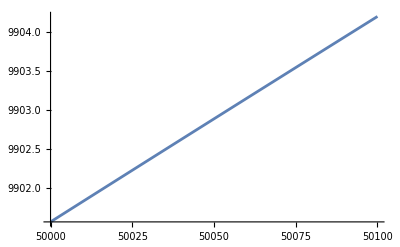

```mathematica
Plot[Integrate[powerVaule[x,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}],{x,50000,50100}]
```

```mathematica
NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]&/@Range[60000,70000,1000]
```

{10018.3,10016.3,10012.3,10006.3,9998.56,9989.06,9977.91,9965.2,9951.02,9935.43,9918.53}

```mathematica
NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]&/@Range[50000,60000,1000]
```

{9901.57,9926.37,9947.88,9966.25,9981.61,9994.12,10003.9,10011.1,10015.8,10018.2,10018.3}

```mathematica
{#,NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]}&/@Range[60000-500,60000+500,100]
```

{{59500,10018.5},{59600,10018.5},{59700,10018.5},{59800,10018.5},{59900,10018.4},{60000,10018.3},{60100,10018.2},{60200,10018.1},{60300,10017.9},{60400,10017.8},{60500,10017.6}}

```mathematica
Sort[{{1,2},{2,0}},Last]
```

{{1,2},{2,0}}

```mathematica
SortBy[%111,Last]
```

{{60500,10017.6},{60400,10017.8},{60300,10017.9},{60200,10018.1},{60100,10018.2},{60000,10018.3},{59900,10018.4},{59800,10018.5},{59700,10018.5},{59500,10018.5},{59600,10018.5}}

```mathematica
{#,NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]}&/@Range[59600-50,59600+50,10]//SortBy[#,Last]&
```

{{59650,10018.5},{59640,10018.5},{59630,10018.5},{59620,10018.5},{59610,10018.5},{59600,10018.5},{59590,10018.5},{59580,10018.5},{59570,10018.5},{59550,10018.5},{59560,10018.5}}

```mathematica
{#,NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]}&/@Range[59450-5,59450+5,1]
```

{{59445,10018.5},{59446,10018.5},{59447,10018.5},{59448,10018.5},{59449,10018.5},{59450,10018.5},{59451,10018.5},{59452,10018.5},{59453,10018.5},{59454,10018.5},{59455,10018.5}}

```mathematica
FoldList[SortBy[{#,NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]}&/@Range[#1-#2,#1+#2,#2/10],Last][[-1,1]]&,50000,10^#&/@Range[4,-2,-1]]
```

{50000,60000,59600,59560,59558,119115/2,2977871/50,11911483/200}

```mathematica
11911483/200//N
```

59557.4

```mathematica
(NIntegrate[powerVaule[#,1,t],{t,30 (2Pi)/ω,40 (2Pi)/ω}]&@(11911483/200))/(40 (2Pi)/ω-30 (2Pi)/ω)
```

315.806

```mathematica
Fold[b,x,{1,2,3}]
```

b[b[b[x,1],2],3]

```mathematica
{{59445,10018.50904304052},{59446,10018.509214611808},{59447,10018.509461786016},{59448,10018.509707071582},{59449,10018.50994185599},{59450,10018.510174456525},{59451,10018.51046448632},{59452,10018.51053477906},{59453,10018.51076092717},{59454,10018.510984918043},{59455,10018.511206740432}}[[-1,1]]
```

59455

# Back up&experiment

## 回收站

```mathematica
workVaule[x_,y_]:=Block[{kdv=x,kdh=y},
With[
{movesDyn=NDSolve[eqnsApp[t]~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},{t,0,100},MaxStepSize->0.01]},
With[{x1=movesDyn[[1,1,2]],x2=movesDyn[[1,2,2]],th1=movesDyn[[1,3,2]],th2=movesDyn[[1,4,2]]},
Integrate[kdv(x1'[t]-x2'[t])^2+2kdh(th1'[t]-th2'[t])^2 ,{t,0,100}]
]]]
```

```mathematica
workVaule[x,y]
```

NDSolve::ndnum: 在 t == 0. 处碰到一个导数的非数值量.

∫_0^100 (2 y (-((J1+Ji) th1''[t])'[t]+((M+mi) x1''[t])'[t])^2+x (-(((h^2 m)/12+(m R^2)/4+m (h/2+x2[t])^2) th2''[t])'[t]+(m x2''[t])'[t])^2)ⅆt

```mathematica
ListPlot3D@Flatten[%95,1]
```

-Graphics3D-

```mathematica
fd1[t_](*阻尼器阻尼力1*):=kd(x1'[t]-x2'[t]);
fd2[t_](*阻尼器阻尼力2*):=kd √Abs[x1'[t]-x2'[t]] Sign[x1'[t]-x2'[t]];
fboncy[x_](*浮力恢复力*):=Piecewise[{{-ρ g Pi R^2 x,x<=h0},{-ρ g Pi R^2 h0-(Pi R^2 H2)/3(1-(H2+h0-x)^3/H2^3),h0<x<H2+h0}},(M+m)g];
smallEqn(*振子运动方程*)[t_]:=m x2''[t]==fd1[t]+kv(+x1[t]-x2[t])g;
bigEqn(*浮子运动方程*)[t_]:=(m1+M)x1''[t]==-fd1[t]-kv(x1[t]-x2[t])+fboncy[x1[t]]+f Cos[ω1 t];
```

```mathematica
With[{x1=movesApp[[1,1,2]],x2=movesApp[[1,2,2]],th1=movesApp[[1,3,2]],th2=movesApp[[1,4,2]]},
NIntegrate[kdv(x1'[t]-x2'[t])^2+2kdh(th1'[t]-th2'[t])^2 ,{t,0,100}]
]//Timing
```

{0.03125,4974.36}

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[eqnsApp[t]~Join~{x1[0]==0,x2[0]==0,th1[0]==0,th2[0]==0,x1'[0]==0,x2'[0]==0,th1'[0]==0,th2'[0]==0},{x1,x2,th1,th2},t]
```

$Aborted

## 运动方程的化简

```mathematica
Clear["Global`*"]
```

```mathematica
(*浮子转动 (bigPitch)*)bigPitch=l Cos[omega1 t]-kx omega1-kj theta1-2 ksP (theta1-theta2)-2 kdP (omega1-omega2)==(J1+Ji) alpha1;

(*振子转动 (smallPitch)*)
smallPitch=2 ksP (theta1-theta2)+2 kdP (omega1-omega2)+m g Sin[theta1] r2==J2 alpha2; (*Assuming thetaP is the angle for mg sin(theta) term in smallPitch*)

(*浮子平动 (bigHeave)*)
bigHeave=-M g+Fbuoy-Fsp Cos[theta2]-gammav v1==M a1;

(*振子平动 (smallHeave)*)
smallHeave=-m g Cos[theta2]+m omega^2 r2+Fsp==m a2;
Fsp=kv(r2-l0-r0);
```

```mathematica
Reduce[{bigPitch,smallPitch,bigHeave,smallHeave},{r0,omega1,omega2,theta1,theta2,alpha1,alpha2,a1,a2,v1,v2,r2}]
```

$Aborted

## experiment

```mathematica
-M g+Fb[x1[t]]-Γv1 x1'[t]==(M+mi)x1''[t]
```

-39271.5+π (2.00001-x1[t])-528.502 x1'[t]==5957.1 x1''[t]

```mathematica
-M g+Fb[x1[t]]-Γv1 x1'[t]+f Cos[w t]==(M+mi)x1''[t]
```

-39271.5+1760 Cos[1.9806 t]+π (2.00001-x1[t])-528.502 x1'[t]==5957.1 x1''[t]

```mathematica
DSolve[{bigHeaveEqn[t]}~Join~initConditions[[1;;2]],x1[t],t]
```

{{x1[t]→0.00635731 ⅇ^(-0.088718 t) (-165938. ⅇ^(0.00640704 t)+2.13196×10^6 ⅇ^(0.0823109 t)-1.96601×10^6 ⅇ^(0.088718 t)-11.8249 ⅇ^(0.088718 t) Cos[1.9806 t]+0.529751 ⅇ^(0.088718 t) Sin[1.9806 t])}}

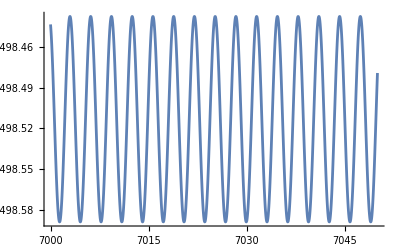

```mathematica
Plot[0.006357306548129446 ⅇ^(-0.08871798168873808 t) (-165937.68729295186 ⅇ^(0.00640704079020848 t)+2.131957145950513*^6 ⅇ^(0.0823109408985296 t)-1.966007633721996*^6 ⅇ^(0.08871798168873808 t)-11.824935565345767 ⅇ^(0.08871798168873808 t) Cos[1.9806 t]+0.5297513241222305 ⅇ^(0.08871798168873808 t) Sin[1.9806 t]),{t,7000,7050}]
```

```mathematica
(*原初的方程*)
```

```mathematica
smallHeave[t_]:=Fpto[t]-m g Cos[th1[t]+th2[t]]-2m r2[t] th1'[t] th2'[t]+m r2[t] th1'[t]^2+m*ai1[t]~Dot~OP[t]==m(r2''[t]-th2'[t]^2r2[t]);
smallSpin[t_]:=m Norm@(ai1[t]~Cross~OP[t])r2[t]+m (2th1[t]r2'[t]-th1''[t]r2[t])+2Lpto[t]==J2[t] th2''[t];
bigHeave[t_]:=F波[t]-M g+F浮[t]-Fpto[t]Cos[th1[t]+th2[t]]+F兴阻[t]==(M+mi)x1''[t];
bigSpin[t_]:=-2Lpto[t]+L波[t]+L兴阻[t]+L静恢[t]==(J1+Ji)th1''[t];
```

#### 二级函数

```mathematica
Fpto[t_]:=kv(r2[t]-l0-h/2)(*劲度系数x(r2-弹簧原长-振子长度一半)*)+kdv r2'[t]
```

```mathematica
ai1[t_]:=D[{0,x1[t]}+Hg{Sin[th1[t]],-Cos[th1[t]]},{t,2}]~Join~{0}
```

```mathematica
OP[t_]:={Cos[Pi/2+th2[t]+th1[t]],Sin[Pi/2+th2[t]+th1[t]],0};
```

```mathematica
F波[t_]:=f Cos[ω t]
```

```mathematica
F浮[t_]:=ρ g( (Pi R^2 H2)/3+Pi R^2 (h0-x1[t]))
```

```mathematica
F兴阻[t_]:=-Γv1 x1'[t]
```

```mathematica
Lpto[t_]:=-kdh(th2'[t])
```

```mathematica
L波[t_]:=L Cos[ω t]
```

```mathematica
L兴阻[t_]:=-Γh1 th1'[t]
```

```mathematica
L静恢[t_]:=-kw th1[t]
```

```mathematica
(*支架高度*)rframe=0;
```

```mathematica
Hg(*浮子重心(距离底面的高度)*)=With[{m1=π R √(R^2+H2^2),m2=2 π R H1,m3=π R^2,h1=-(∫_0^H2 (x 2 π x R √(R^2+H2^2))/(H2 H2)ⅆx)/(∫_0^H2 (2 π x R √(R^2+H2^2))/(H2 H2)ⅆx),h2=H1/2,h3=H1},(m1 h1+m2 h2+m3 h3)/(m1+m2+m3)]
```

1.36668

```mathematica
σ=M/(2Pi R H1+Pi R^2+π R √(R^2+H2^2))
```

187.051

```mathematica
J1=With[{M1=σ π R √(R^2+H2^2)},M1 (R^2/4+H2^2/18)+M1 (Hg-H2/3)^2+2 π R H1 σ (R^2/2+H1^2/12+(Hg-H1/2)^2)+σ π R^2 (R^2/4+(H1-Hg)^2)]
```

7310.

```mathematica
J2[t_]:=(1/4 m R^2+1/12 m h^2)+m(r2[t]+h/2)^2
```

```mathematica
(*初始吃水线距离圆柱底面的距离*)h0=x/.First@Solve[(M+m)g==ρ g ((Pi R^2 H2)/3+Pi R^2 x),x]
```

2.00001

```mathematica
x0(*弹簧的初始长度*)=x/.Solve[kv (l0-x)==m g,x][[1]]
```

0.201957

## 只考虑浮子的平动与转动

### 计算

```mathematica
Fb[x_]:=ρ g( (Pi R^2 H2)/3+Pi R^2 (h0-x));
```

```mathematica
initConditions={x1[0]==0,x1'[0]==0,th1[0]==0,th1'[0]==0};
```

```mathematica
bigSpinEqn[t_]:=L Cos[w t]-Γh1 th1'[t]-kw th1[t]==(Ji+J1)th1''[t];
bigHeaveEqn[t_]:=-M g+Fb[x1[t]]-Γv1 x1'[t]+f Cos[w t]==(M+mi+m)x1''[t];
```

```mathematica
(m1+M)x1''[t]==fb[x1[t]]+f Cos[ω1 t]-M g+fwaved[t]
```

```mathematica
bigMove=NDSolve[{bigHeaveEqn[t],bigSpinEqn[t]}~Join~initConditions,{x1,th1},{t,0,200}]
```

{{x1→InterpolatingFunction[…],th1→InterpolatingFunction[…]}}

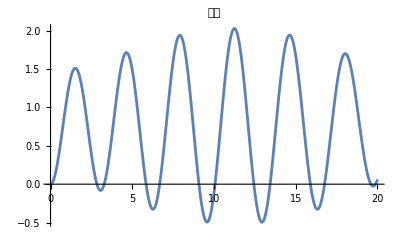
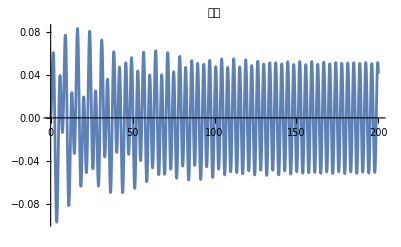

```mathematica
With[{x1=bigMove[[1,1,2]],th1=bigMove[[1,2,2]]},
Row[{Plot[x1[t],{t,0,20},PlotLabel->"垂荡"],Plot[th1[t],{t,0,200},PlotLabel->"纵摇"]}]
]
```

```mathematica
5/360 Pi//N
```

0.0436332

### 动画

```mathematica
With[{x1=bigMove[[1,1,2]],th1=bigMove[[1,2,2]]},
Animate[Show[
Graphics[Point[{{0,x1[t]},{0,x1[t]}-(Hg+H2){Sin[th1[t]],Cos[th1[t]]}}]](*重心的垂荡(无纵摇)*),
Graphics[Line[{{0,x1[t]},{0,x1[t]}-(Hg+H2){Sin[th1[t]],Cos[th1[t]]}}]],
ContourPlot[y==0-Hg+h0,{x,-1,1},{y,-0.5,4}],
PlotRange->{{-1,1},{-2,1.5}},Axes->{False,True}
],{t,0,100}]]
```

## 受力计算

```mathematica
Clear["Global`*"]
```

```mathematica
xo[t_](*o点x坐标*):=Gx[t]-G1O Sin[θ1[t]];
D[xo[t],{t,#}]&/@{0,1,2}//TableForm//TraditionalForm
```

Gx(t)-G1O sin(θ1(t))
Gx'(t)-G1O θ1'(t) cos(θ1(t))
Gx''(t)-G1O (θ1''(t) cos(θ1(t))-(θ1'(t))^2 sin(θ1(t)))

```mathematica
yo[t_](*o点y坐标*):=Gy[t]-G1O Cos[θ1[t]];
D[yo[t],{t,#}]&/@{0,1,2}//TableForm//TraditionalForm
```

Gy(t)-G1O cos(θ1(t))
G1O θ1'(t) sin(θ1(t))+Gy'(t)
Gy''(t)-G1O ((θ1'(t))^2 (-cos(θ1(t)))-θ1''(t) sin(θ1(t)))

```mathematica
ao[t_]:={D[xo[t],{t,2}],D[yo[t],{t,2}]}
```

```mathematica
ao[t]
```

{Gx''[t]-G1O (-Sin[θ1[t]] θ1'[t]^2+Cos[θ1[t]] θ1''[t]),Gy''[t]-G1O (-Cos[θ1[t]] θ1'[t]^2-Sin[θ1[t]] θ1''[t])}

```mathematica
Fc[t_]:=-m ao[t]
```

```mathematica
FcOnR[t_]:=With[{rr={-Sin[θ2[t]+θ1[t]],Cos[θ2[t]+θ1[t]]},rt={-Cos[θ2[t]-θ1[t]],-Sin[θ2[t]-θ1[t]]}},Fc[t]~Dot~#&/@{rr,rt}]
```

```mathematica
FcOnR[t]//FullSimplify//TraditionalForm
```

{-m (G1O θ1''(t) sin(θ1+θ2+θ1(t))+G1O (θ1'(t))^2 cos(θ1+θ2+θ1(t))-Gx''(t) sin(θ1+θ2)+Gy''(t) cos(θ1+θ2)),-m (G1O θ1''(t) cos(θ1-θ2-θ1(t))+G1O (θ1'(t))^2 sin(θ1-θ2-θ1(t))-Gx''(t) cos(θ1-θ2)+Gy''(t) sin(θ1-θ2))}

a_i1, 第一个虚拟力

```mathematica
FcOnR[t]/.{Gx''[t]->0,G1O->lGO}//FullSimplify
```

{-m (lGO Cos[2 θ1[t]+θ2[t]] θ1'[t]^2+Cos[θ1[t]+θ2[t]] Gy''[t]+lGO Sin[2 θ1[t]+θ2[t]] θ1''[t]),m (lGO Sin[θ2[t]] θ1'[t]^2-Sin[θ1[t]-θ2[t]] Gy''[t]-lGO Cos[θ2[t]] θ1''[t])}

## 列方程: 表达式

### 导入方程与函数

#### 四个主方程

```mathematica
Clear["Global`*"]
```

```mathematica
smallHeave[t_]:=-Fpto[t]-m g Cos[th1[t]+th2[t]]-2m r2[t] th1'[t] th2'[t]+m r2[t] th1'[t]^2(*+m*ai1[t]~Dot~OP[t]*)==m(r2''[t]-th2'[t]^2r2[t]);
smallSpin[t_]:=m Norm@(ai1[t]~Cross~OP[t])r2[t]+m (2th1[t]r2'[t]-th1''[t]r2[t])+2Lpto[t]==J2[t] th2''[t];
bigHeave[t_]:=F波[t]-M g+F浮[t]-Fpto[t]Cos[th1[t]+th2[t]]+F兴阻[t]==(M+mi)x1''[t];
bigSpin[t_]:=-2Lpto[t]+L波[t]+L兴阻[t]+L静恢[t]==(J1+Ji)th1''[t];
```

```mathematica
eqns[t]//TableForm
```

-23843.4 Cos[th1[t]+th2[t]]-80000 (-0.75+r2[t])-10000 r2'[t]+2433 r2[t] th1'[t]^2-4866 r2[t] th1'[t] th2'[t]+2433 (-1.36668 Sin[th1[t]+th2[t]] (-Sin[th1[t]] th1'[t]^2+Cos[th1[t]] th1''[t])+Cos[th1[t]+th2[t]] (-1.36668 (-Cos[th1[t]] th1'[t]^2-Sin[th1[t]] th1''[t])+x1''[t]))==2433 (-r2[t] th2'[t]^2+r2''[t])
2433 √(0.+Abs[-1.36668 Cos[th1[t]+th2[t]] Sin[th1[t]] th1'[t]^2+1.36668 Cos[th1[t]] Sin[th1[t]+th2[t]] th1'[t]^2+1.36668 Cos[th1[t]] Cos[th1[t]+th2[t]] th1''[t]+1.36668 Sin[th1[t]] Sin[th1[t]+th2[t]] th1''[t]+Sin[th1[t]+th2[t]] x1''[t]]^2) r2[t]+2 (-250000 th2[t]-10000 th2'[t])+2433 (2 th1[t] r2'[t]-r2[t] th1''[t])==(658.938+2433 (0.25+r2[t])^2) th2''[t]
-47686.8+3640 Cos[1.7152 t]+10045. (0.837758+π (2.00001-x1[t]))-Cos[th1[t]+th2[t]] (80000 (-0.75+r2[t])+10000 r2'[t])-683.456 x1'[t]==5894.88 x1''[t]
1690 Cos[1.7152 t]-8890.7 th1[t]-654.338 th1'[t]-2 (-250000 th2[t]-10000 th2'[t])==14311.9 th1''[t]

#### 二级函数

```mathematica
Fpto[t_]:=kv(r2[t]-l0-h/2)(*劲度系数x(r2-弹簧原长-振子长度一半)*)+kdv r2'[t]
```

```mathematica
ai1[t_]:=D[{0,x1[t]}+Hg{Sin[th1[t]],-Cos[th1[t]]},{t,2}]~Join~{0}
```

```mathematica
OP[t_]:={Cos[Pi/2+th2[t]+th1[t]],Sin[Pi/2+th2[t]+th1[t]],0};
```

```mathematica
F波[t_]:=f Cos[ω t]
```

```mathematica
F浮[t_]:=ρ g( (Pi R^2 H2)/3+Pi R^2 (h0-x1[t]))
```

```mathematica
F兴阻[t_]:=-Γv1 x1'[t]
```

```mathematica
Lpto[t_]:=-kdh(th2'[t])-kh th2[t]
```

```mathematica
L波[t_]:=L Cos[ω t]
```

```mathematica
L兴阻[t_]:=-Γh1 th1'[t]
```

```mathematica
L静恢[t_]:=-kw th1[t]
```

### 验证与计算

```mathematica
{{"振子平动","振子转动","浮子平动","浮子转动"},{smallHeave[t],
smallSpin[t],
bigHeave[t],
bigSpin[t]}}/.{th1->θ1,th2->θ2}//Transpose//TableForm//TraditionalForm
```

振子平动 | 10000 r2'(t)-4866 r2(t) θ1'(t) θ2'(t)+2433 r2(t) (θ1'(t))^2+80000 (r2(t)-0.75)-23843.4 cos(θ1(t)+θ2(t))+2433 (cos(θ1(t)+θ2(t)) (x1''(t)-1.36668 ((θ1'(t))^2 (-cos(θ1(t)))-θ1''(t) sin(θ1(t))))-1.36668 sin(θ1(t)+θ2(t)) (θ1''(t) cos(θ1(t))-(θ1'(t))^2 sin(θ1(t))))==2433 (r2''(t)-r2(t) (θ2'(t))^2)
振子转动 | 2433 r2(t) √(Abs[-1.36668 cos(θ1(t)+θ2(t)) sin(θ1(t)) (θ1'(t))^2+1.36668 cos(θ1(t)) sin(θ1(t)+θ2(t)) (θ1'(t))^2+sin(θ1(t)+θ2(t)) x1''(t)+1.36668 cos(θ1(t)) cos(θ1(t)+θ2(t)) θ1''(t)+1.36668 sin(θ1(t)) sin(θ1(t)+θ2(t)) θ1''(t)]^2+0.)+2433 (2 θ1(t) r2'(t)-r2(t) θ1''(t))-20000 θ2'(t)==(2433 (r2(t)+0.25)^2+658.938) θ2''(t)
浮子平动 | 10045. (π (2.00001-x1(t))+0.837758)-(10000 r2'(t)+80000 (r2(t)-0.75)) cos(θ1(t)+θ2(t))-683.456 x1'(t)+3640 cos(1.7152 t)-47686.8==5894.88 x1''(t)
浮子转动 | -654.338 θ1'(t)-8890.7 θ1(t)+20000 θ2'(t)+1690 cos(1.7152 t)==14311.9 θ1''(t)

```mathematica
{smallHeave[t],
smallSpin[t],
bigHeave[t],
bigSpin[t]}/.{th1->θ1,th2->θ2}//TableForm
```

-23843.4 Cos[θ1[t]+θ2[t]]+80000 (-0.75+r2[t])+10000 r2'[t]+2433 r2[t] θ1'[t]^2-4866 r2[t] θ1'[t] θ2'[t]+2433 (-1.36668 Sin[θ1[t]+θ2[t]] (-Sin[θ1[t]] θ1'[t]^2+Cos[θ1[t]] θ1''[t])+Cos[θ1[t]+θ2[t]] (x1''[t]-1.36668 (-Cos[θ1[t]] θ1'[t]^2-Sin[θ1[t]] θ1''[t])))==2433 (-r2[t] θ2'[t]^2+r2''[t])
2433 √(0.+Abs[-1.36668 Cos[θ1[t]+θ2[t]] Sin[θ1[t]] θ1'[t]^2+1.36668 Cos[θ1[t]] Sin[θ1[t]+θ2[t]] θ1'[t]^2+Sin[θ1[t]+θ2[t]] x1''[t]+1.36668 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ1''[t]+1.36668 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ1''[t]]^2) r2[t]-20000 (θ1'[t]-θ2'[t])+2433 (2 θ1[t] r2'[t]-r2[t] θ1''[t])==(658.938+2433 (0.25+r2[t])^2) θ2''[t]
-47686.8+3640 Cos[1.7152 t]+10045. (0.837758+π (2.00001-x1[t]))-Cos[θ1[t]+θ2[t]] (80000 (-0.75+r2[t])+10000 r2'[t])-683.456 x1'[t]==5894.88 x1''[t]
1690 Cos[1.7152 t]-8890.7 θ1[t]-654.338 θ1'[t]+20000 (θ1'[t]-θ2'[t])==14311.9 θ1''[t]

```mathematica
eqns[t]
```

{-23843.4 Cos[th1[t]+th2[t]]+80000 (-0.75+r2[t])+10000 r2'[t]+2433 r2[t] th1'[t]^2-4866 r2[t] th1'[t] th2'[t]+2433 (-1.36668 Sin[th1[t]+th2[t]] (-Sin[th1[t]] th1'[t]^2+Cos[th1[t]] th1''[t])+Cos[th1[t]+th2[t]] (-1.36668 (-Cos[th1[t]] th1'[t]^2-Sin[th1[t]] th1''[t])+x1''[t]))==2433 (-r2[t] th2'[t]^2+r2''[t]),-2433 √(0.+Abs[-1.36668 Cos[th1[t]+th2[t]] Sin[th1[t]] th1'[t]^2+1.36668 Cos[th1[t]] Sin[th1[t]+th2[t]] th1'[t]^2+1.36668 Cos[th1[t]] Cos[th1[t]+th2[t]] th1''[t]+1.36668 Sin[th1[t]] Sin[th1[t]+th2[t]] th1''[t]+Sin[th1[t]+th2[t]] x1''[t]]^2) r2[t]-20000 th2'[t]==(658.938+2433 (0.25+r2[t])^2) th2''[t],-47686.8+3640 Cos[1.7152 t]+10045. (0.837758+π (2.00001-x1[t]))-Cos[th1[t]+th2[t]] (80000 (-0.75+r2[t])+10000 r2'[t])-683.456 x1'[t]==5894.88 x1''[t],1690 Cos[1.7152 t]-8890.7 th1[t]-654.338 th1'[t]+20000 th2'[t]==14311.9 th1''[t]}

## 解方程

```mathematica
smallHeave[t_]:=-Fpto[t]-m g Cos[th1[t]+th2[t]]-2m r2[t] th1'[t] th2'[t]+m r2[t] th1'[t]^2+m*ai1[t]~Dot~OP[t]==m(r2''[t]-th2'[t]^2r2[t]);
smallSpin[t_]:=m Norm@(ai1[t]~Cross~OP[t])r2[t]+m (2th1[t]r2'[t]-th1''[t]r2[t])+2Lpto[t]==J2[t] th2''[t];
bigHeave[t_]:=F波[t]-M g+F浮[t]-Fpto[t]Cos[th1[t]+th2[t]]+F兴阻[t]==(M+mi)x1''[t];
bigSpin[t_]:=-2Lpto[t]+L波[t]+L兴阻[t]+L静恢[t]==(J1+Ji)th1''[t];
```

```mathematica
eqns[t_]:={smallHeave[t],smallSpin[t],bigHeave[t],bigSpin[t]}
vars={th1,th2,x1,r2};
init={x1[0]==0,r2[0]==x0,th1[0]==0,th2[0]==0,x1'[0]==0,r2'[0]==0,th1'[0]==0,th2'[0]==0};
```

```mathematica
moves=NDSolve[eqns[t]~Join~init,vars,{t,0,10},MaxStepSize->0.0001]//AbsoluteTiming
```

{0.619381,{{th1→InterpolatingFunction[{{0., 10.}}, <>],th2→InterpolatingFunction[{{0., 10.}}, <>],x1→InterpolatingFunction[{{0., 10.}}, <>],r2→InterpolatingFunction[{{0., 10.}}, <>]}}}

```mathematica
Dynamic[Plot[#[[2]][t],{t,0,10},PlotLabel->#[[1]]]&/@moves[[2,1]]//Column]
```